{{AR→0,AL→2^(1/4),BR→2^(1/4),BL→0}}

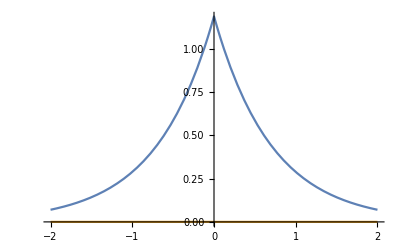

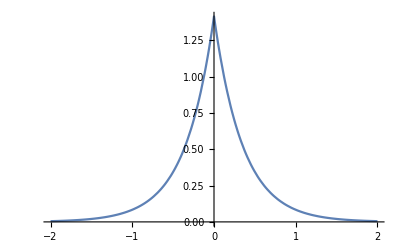

```mathematica
m=1;
Ē=-1;
ћ=1;
k=(√(2m Ē))/ћ;
κ=-I k;
z=√κ;
V=(I k ћ^2)/m;
s=Solve[AR+AL==BR+BL&&AR-AL-BR+BL==(2I m V/(k ћ^2))(AR+AL)&&AR==0&&AL==z,{AR,AL,BR,BL}]
Plot[{Piecewise[{{Re[AR Exp[I k x]+AL Exp[-I k x]]/.s,x<0},{Re[BR Exp[I k x]+BL Exp[-I k x]]/.s,x>0}}],Piecewise[{{Im[AR Exp[I k x]+AL Exp[-I k x]]/.s,x<0},{Im[BR Exp[I k x]+BL Exp[-I k x]]/.s,x>0}}]},{x,-2,2}]
Plot[Piecewise[{{Abs[AR Exp[I k x]+AL Exp[-I k x]]^2/.s,x<0},{Abs[BR Exp[I k x]+BL Exp[-I k x]]^2/.s,x>0}}],{x,-2,2}]
```